```mathematica
dd[n_, z_] := (-1)^z ((1-Gamma[ z, -Log[n]])/Gamma[z])
```

```mathematica
dd[100]
```

```mathematica
dd[100,2.]
```

361.517-1.32697×10^-13 ⅈ

```mathematica
dd[100,0]
```

0

```mathematica
FullSimplify[D[dd[100,z],z]]
```

1/Gamma[z](-1)^z (ⅈ π-MeijerG[{{},{1,1}},{{0,0,z},{}},-2 Log[10]]-PolyGamma[0,z]+Gamma[z,-2 Log[10]] (-2 ⅈ π-Log[Log[100]]+PolyGamma[0,z]))

```mathematica
1/Gamma[z](-1)^z (ⅈ π-MeijerG[{{},{1,1}},{{0,0,z},{}},-2 Log[10]]-PolyGamma[0,z]+Gamma[z,-2 Log[10]] (-2 ⅈ π-Log[Log[100]]+PolyGamma[0,z]))/.z->0
```

Infinity::indet: Indeterminate expression ⅈ\ π + ComplexInfinity + ComplexInfinity - MeijerG[{{}, {1, 1}}, {{0, 0, 0}, {}}, -2\ Log[10]] encountered.

Indeterminate

```mathematica
dd[100,.5]
```

-1.73281-0.576858 ⅈ

```mathematica
ddd[n_, z_, d_] := (dd[n,z+d]-dd[n,z-d])/(2d)
```

```mathematica
ddd[100,0,.000001]
```

31.1261+3.14159 ⅈ

```mathematica
LogIntegral[100.]
```

30.1261

```mathematica
-Gamma[0, -Log[100.]]
```

30.1261+3.14159 ⅈ

```mathematica
eee[100,3,2]
```

71

```mathematica
eee[n_, k_, c_] := eee[n,k,c] = Sum[ eee[Floor[n/j],k-1,c],{j,c+1, n}]/c;eee[n_, 0, c_] := eee[n,0,c]=1
Dd[n_,0,a_]:=Dd[n,0,a]=1;Dd[n_,1,a_]:=Dd[n,1,a]=Floor[n]-a+1
Dd[n_,k_,a_]:=Dd[n,k,a]=Sum[Binomial[k,j] Dd[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
ef[n_, k_, c_] := eee[ n c^k, k, c]
df[n_, k_, c_] := If[ n c^k < (c+1)^k, 0, Dd[ n c^k, k, c+1]/c^k]
pf[n_, c_] := Sum[ (-1)^(k+1)/k df[ n, k, c],{k,1, 100}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
bf[n_, z_, c_] := Expand[Sum[ bin[z,k] df[ n, k, c],{k,1, 100}]]
zeros[n_, c_] := List@@NRoots[ bf[n,z, c]==0,z][[All,2]]
lp[n_,c_] := RootLocusPlot[1/bf[n,z,c],{k,0,1}]
```

```mathematica
df[100,50,20]
```

26128734561791570755717594093/112589990684262400000000000000000000000000000000000000000000000000

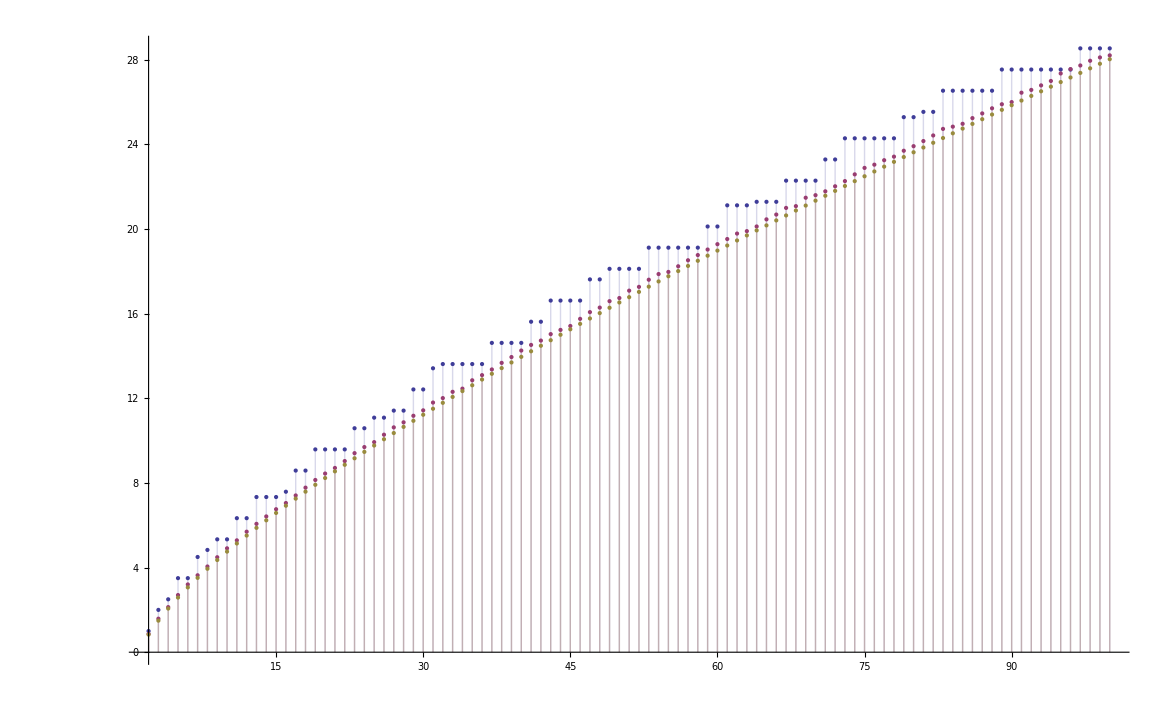

```mathematica
DiscretePlot[{pf[n,1], pf[n,6], LogIntegral[n]-Log[Log[n]]-EulerGamma},{n,2,100}]
```

```mathematica
bf[10,z, 20]
```

```mathematica
LogIntegral[10.]-Log[Log[10.]]-EulerGamma
```

4.75435